```mathematica
Rtot=1
d=2
q=0

Lint[Rtot_,q_]:=(2*q+1)/(2*Rtot)NIntegrate[(LegendreP[q,Cos[x]] LegendreP[q,Cos[y]] Sin[x] Sin[y])/(√(2 -2  Sin[x] Sin[y] Cos[p]-2  Cos[x] Cos[y])),{x,0,π},{y,0,π},{p,0,2 π}]

Lintimage[Rtot_,q_,d_]:=NIntegrate[((2*q+1)*LegendreP[q,Cos[x1]] LegendreP[q,Cos[y1]] Sin[x1] Sin[y1])/(2*Rtot √(2 -2  Sin[x1] Sin[y1] Cos[φ]-4*(d/Rtot)*(Cos[x1]+Cos[y1])+2* Cos[x1] Cos[y1]+4*d*d/(Rtot*Rtot))),{x1,0,π},{y1,0,π},{φ,0,2 π}, MaxRecursion->20, Method->{GlobalAdaptive,MaxErrorIncreases->20000}]
```

```mathematica
Integrate[(LegendreP[q,Cos[x]] LegendreP[q,Cos[y]] Sin[x] Sin[y])/(√(2 -2  Sin[x] Sin[y] Cos[p]-2  Cos[x] Cos[y])),{p,0,2π}, Assumptions -> x ∈ Reals &&y ∈Reals]
```

Integrate[(LegendreP[q,Cos[x]] LegendreP[q,Cos[y]] Sin[x] Sin[y])/(√(2-2 Cos[x] Cos[y]-2 Cos[p] Sin[x] Sin[y])),{p,0,2 π},Assumptions→x∈Reals&&y∈Reals]

```mathematica
Integrate[ a/(√2*√(1 - b Cos[p] - c)), {p,0,2π}, Assumptions-> a∈Reals && b∈Reals && c∈Reals]
```

ConditionalExpression[(a ((2 EllipticK[(2 b)/(1+b-c)])/(√(1+b-c))+(2 EllipticK[(2 b)/(-1+b+c)])/(√(1-b-c))))/(√2),1+b>c&&b+c<1]

```mathematica
DLintimage[L_,q_,d_]:=NIntegrate[((2*q+1)*LegendreP[q,Cos[x1]] LegendreP[q,Cos[y1]] Sin[x1] Sin[y1]*(2*L-2*L*Sin[x1]*Sin[y1]*Cos[p]-4*d*(Cos[x1])+2*L*Cos[x1]*Cos[y1]))/(2*(L √(2 -2  Sin[x1] Sin[y1] Cos[p]-4*(d/L)*(Cos[x1]+Cos[y1])+2* Cos[x1] Cos[y1]+4*d*d/(L*L)))^3),{x1,0,π},{y1,0,π},{p,0,2 π},MaxRecursion->20, Method->{GlobalAdaptive,MaxErrorIncreases->20000}]
```

```mathematica
Lintimage[L,1,2]
```

0.1309

```mathematica
DLintimage[L,0,2]
```

0.

```mathematica
eps=80
```

80

```mathematica
fs={0,0,0,0,0,0,0,0}
```

{0,0,0,0,0,0,0,0}

```mathematica
{0,0,0,0}
d=5
```

{0,0,0,0}

```mathematica
d=2
q=3
```

2

3

```mathematica
d=2
```

2

```mathematica
d
```

4

```mathematica
dz=0.01
```

0.01

```mathematica
0.1
```

```mathematica
d=2
```

2

```mathematica
d=5
(*For[q=0,q<4, q++,
Asubl= -Integrate[(-L+2*d*y1)*LegendreP[q,y1]/(L*L-4*d*L*y1+4*d*d)^(3/2),{y1,1,-1}]*79*Sqrt[(2*q+1)*Pi]/81 + Integrate[LegendreP[q,y1]*Sqrt[(2*q+1)*Pi]/(L*L),{y1,1,-1}];
Print[Asubl];
Csubl = -4*Pi/((2*q+1)*2*L*L)-79*DLintimage[L,q,d]/162;
Print[Csubl];
Bsubl=4*Pi/((2*q+1)*L)+79*Lintimage[L,q,d]/81;
Print[Bsubl];
fsubl=((eps-1)/(4*Pi))^2*L*L*Asubl*Bsubl/eps;

fsubl=fsubl/((eps+1)/2-(eps-1)*L^2*Csubl/(4*Pi));

fs[[q+1]]=Re[fsubl];

Print[fsubl]]*)

For[q=0,q<5, q++,
Asubl= Integrate[(L-2*d*y1+2*dz*y1)*LegendreP[q,y1]/(L*L-4*d*L*y1+4*d*d-4*dz*d+2*L*dz*y1+dz*dz)^(3/2),{y1,1,-1}]*79*Sqrt[(2*q+1)*Pi]/81 + Integrate[LegendreP[q,y1]*Sqrt[(2*q+1)*Pi]*(L-2*dz*y1)/(L*L-2*dz*L*y1+dz*dz)^(3/2),{y1,1,-1}];
Print[Asubl];
Csubl = -4*Pi/((2*q+1)*2*L*L)-79*DLintimage[L,q,d]/162;
Print[Csubl];
Bsubl=4*Pi/((2*q+1)*L)+79*Lintimage[L,q,d]/81;
Print[Bsubl];
fsubl=((eps-1)/(4*Pi))^2*L*L*Asubl*Bsubl/eps;

fsubl=fsubl/((eps+1)/2-(eps-1)*L^2*Csubl/(4*Pi));

fs[[q+1]]=Re[fsubl];

Print[fsubl]]
```

5

-3.54456

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 20000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.9928×10^-10 and 4.34302×10^-9 for the integral and error estimates.

-6.283185307

13.792

-0.301886

-0.000479853

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-2.08622

4.19696

-0.0000185566

0.00294003

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

-1.25634

2.51342

0.0000754281

0.000391862

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 20000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0000215423 and 6.84607×10^-11 for the integral and error estimates.

-0.897587

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 20000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.59039×10^-6 and 1.08415×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

1.7952

7.53159×10^-6

0.0000462821

$Aborted

```mathematica
fs[[4]]
```

7.53159×10^-6

```mathematica
d
```

2

```mathematica
Plot[LegendreP[0,x1], LegendreP[1,x1], LegendreP[2,x1],{x1,1,-1}]
```

Plot::nonopt: Options expected (instead of {x1, 1, -1}) beyond position 2 in Plot[LegendreP[0, x1], LegendreP[1, x1], LegendreP[2, x1], {x1, 1, -1}]. An option must be a rule or a list of rules.

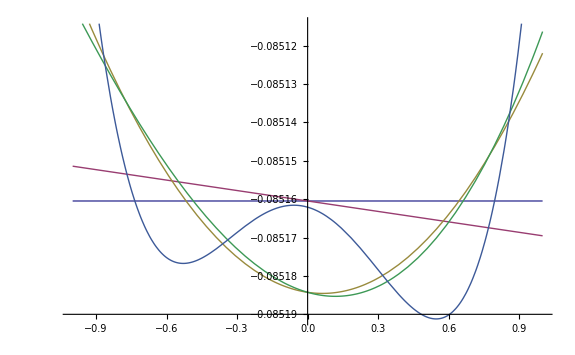

```mathematica
Plot[{fs[[1]]*LegendreP[0,x1]*Sqrt[1/(4*Pi)],fs[[1]]*LegendreP[0,x1]*Sqrt[1/(4*Pi)]+fs[[2]]*LegendreP[1,x1]*Sqrt[3/(4*Pi)], fs[[1]]*LegendreP[0,x1]*Sqrt[1/(4*Pi)]+fs[[2]]*LegendreP[1,x1]*Sqrt[3/(4*Pi)]+fs[[3]]*LegendreP[2,x1]*Sqrt[5/(4*Pi)],fs[[1]]*LegendreP[0,x1]*Sqrt[1/(4*Pi)]+fs[[2]]*LegendreP[1,x1]*Sqrt[3/(4*Pi)]+fs[[3]]*LegendreP[2,x1]*Sqrt[5/(4*Pi)] +fs[[4]]*LegendreP[3,x1]*Sqrt[7/(4*Pi)],fs[[1]]*LegendreP[0,x1]*Sqrt[1/(4*Pi)]+fs[[2]]*LegendreP[1,x1]*Sqrt[3/(4*Pi)]+fs[[3]]*LegendreP[2,x1]*Sqrt[5/(4*Pi)] +fs[[4]]*LegendreP[3,x1]*Sqrt[7/(4*Pi)] +fs[[5]]*LegendreP[4,x1]*Sqrt[9/(4*Pi)]  },{x1,1,-1}]
```

```mathematica
,
```

```mathematica
fs[[1]]
```

-0.338858

```mathematica
f=0
```

0

```mathematica
0
energy=0
```

0

```mathematica
f=0
f2=0
```

0

0

```mathematica
-Sqrt[Pi*(2*q+1)]*(Integrate[LegendreP[q,x1]/(L^2+2*dz*L*x1+dz^2)^(1/2), {x1,1,-1}] + 79*Integrate[LegendreP[q,x1]/(L*L-4*d*L*x1+4*d*d +4*dz*d-2*L*dz*x1+dz*dz)^(1/2),{x1,1,-1}]/81)
```

0.00328463

```mathematica
Integrate[(L-2*d*y1+2*dz*y1)*LegendreP[q,y1]/(L*L-4*d*L*y1+4*d*d-4*dz*d+2*L*dz*y1+dz*dz)^(3/2),{y1,1,-1}]*79*Sqrt[(2*q+1)*Pi]/81 + Integrate[LegendreP[q,y1]*Sqrt[(2*q+1)*Pi]*(L-2*dz*y1)/(L*L-2*dz*L*y1+dz*dz)^(3/2),{y1,1,-1}]
```

-0.0713016

```mathematica
Integrate[(L-2*d*y1-2*dz*y1)*LegendreP[q,y1]/(L*L-4*d*L*y1+4*d*d+4*dz*d-2*L*dz*y1+dz*dz)^(3/2),{y1,1,-1}]*79*Sqrt[(2*q+1)*Pi]/81 + Integrate[LegendreP[q,y1]*Sqrt[(2*q+1)*Pi]*(L+2*dz*y1)/(L*L+2*dz*L*y1+dz*dz)^(3/2),{y1,1,-1}]
```

0.320655

```mathematica
q=3
```

3

```mathematica
f=0
```

0

```mathematica
factor1=0
```

0

```mathematica
factor2=0
```

0

```mathematica
For[q=0,q<4, q++,

Asubl= Integrate[(L-2*d*y1+2*dz*y1)*LegendreP[q,y1]/(L*L-4*d*L*y1+4*d*d-4*dz*d+2*L*dz*y1+dz*dz)^(3/2),{y1,1,-1}]*79*Sqrt[(2*q+1)*Pi]/81 + Integrate[LegendreP[q,y1]*Sqrt[(2*q+1)*Pi]*(L-2*dz*y1)/(L*L-2*dz*L*y1+dz*dz)^(3/2),{y1,1,-1}];
BBsubl=-Sqrt[Pi*(2*q+1)]*(Integrate[LegendreP[q,x1]/(L^2+2*dz*L*x1+dz^2)^(1/2), {x1,1,-1}] + 79*Integrate[LegendreP[q,x1]/(L*L-4*d*L*x1+4*d*d +4*dz*d-2*L*dz*x1+dz*dz)^(1/2),{x1,1,-1}]/81);
CBsubl= Integrate[(L-2*d*y1-2*dz*y1)*LegendreP[q,y1]/(L*L-4*d*L*y1+4*d*d+4*dz*d-2*L*dz*y1+dz*dz)^(3/2),{y1,1,-1}]*79*Sqrt[(2*q+1)*Pi]/81 + Integrate[LegendreP[q,y1]*Sqrt[(2*q+1)*Pi]*(L+2*dz*y1)/(L*L+2*dz*L*y1+dz*dz)^(3/2),{y1,1,-1}];
factor1 =((eps-1)/(4*Pi))^2*Asubl*BBsubl*L^2/eps;
factor2 = (eps-1)*L^2*fs[[q+1]]*CBsubl/(4*Pi);
Print[q, " ",Asubl, " ", BBsubl, " ", CBsubl, " ", factor1,  " ", factor2];
f+=((eps-1)/(4*Pi))^2*Asubl*BBsubl*L^2/eps + (eps-1)*L^2*fs[[q+1]]*CBsubl/(4*Pi);
f2+=factor1+factor2;
energy=f*eps*2*Pi/(eps-1) + (eps-1)/(4*d*(eps+1));
Print[f, energy];
]
```

0 -3.54456 3.8903 -3.54455 -6.81223 6.727

-0.0852351-0.493562

1 -0.000479853 -0.000545209 0.0404022 1.29246×10^-7 -4.71326×10^-6

-0.0852397-0.493591

2 0.00294003 0.00170009 0.00292782 2.46927×10^-6 1.38834×10^-6

-0.0852358-0.493566

3 0.000391862 0.000128815 0.000392201 2.49371×10^-8 1.85701×10^-8

-0.0852358-0.493566

```mathematica
dz
```

0.01

```mathematica
K=(eps-1)/(eps+1)

f1=-((eps-1)/(4*Pi))^2*2*Pi*L^2*Integrate[(-1/L^2+(-L+2*d*x1)*K/(L^2-4*d*x1+4*d*d)^(3/2))*(1/L+K/(L^2-4*d*x1+4*d*d)^(1/2)),{x1,1,-1}]/eps
```

79/81

```mathematica
(*Asubl=-Integrate[(-L+2*d*x1)*LegendreP[q,x1]/(L*L-4*d*L*x1+4*d*d)^(3/2),{x1,1,-1}]*79*Sqrt[(2*q+1)*Pi]/81 + Integrate[LegendreP[q,x1]*Sqrt[(2*q+1)*Pi]/(L*L),{x1,1,-1}];*)
```

```mathematica
(*CBsubl=Sqrt[Pi*(2*q+1)]*(Integrate[LegendreP[q,x1]/(L^2), {x1,1,-1}] + 79*Integrate[LegendreP[q,x1]*(L-2*d*x1)/(L*L-4*d*L*x1+4*d*d)^(3/2),{x1,1,-1}]/81);*)
```

-7.73003

```mathematica
-7.72173+0.00768913+0.000576685
f2=-(eps-1)/(4*Pi)*2*Pi*L^2*(Integrate[(fs[[1]]*LegendreP[0,x1]*Sqrt[1/(4*Pi)]+fs[[2]]*LegendreP[1,x1]*Sqrt[3/(4*Pi)]+fs[[3]]*LegendreP[2,x1]*Sqrt[5/(4*Pi)])*(-1/L^2 + (L-2*d*x1)*K/(L^2-4*d*x1+4*d*d)^(3/2)),{x1,1,-1}])
```

-7.71346

21.9771

```mathematica
7.621257135001858-7.73003
```

-0.108773

```mathematica
7.625204082923290-7.73003
```

-0.104826

```mathematica
N[-(6241 (4017016+93615 Log[9]-93615 Log[25]))/(1007769600 π)]
```

-7.73003

```mathematica
N[-561928649599/(354294000 π)]
```

```mathematica
-504.8559797717965/80
```

-6.3107

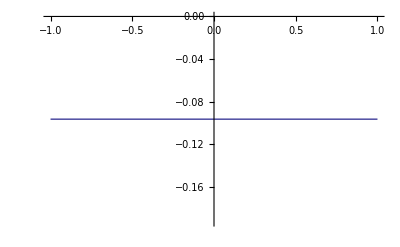

```mathematica
Plot[fs[[1]]*LegendreP[0,x1]*Sqrt[1/(4*Pi)],{x1,1,-1}]
```

```mathematica
f2=-(eps-1)/(4*Pi)*2*Pi*L^2*(Integrate[(fs[[3]]*LegendreP[2,x1]*Sqrt[5/(4*Pi)])*(-1/L^2 + (L-2*d*x1)*K/(L^2-4*d*x1+4*d*d)^(3/2)),{x1,1,-1}])
```

-0.000380083

```mathematica
Integrate[LegendreP[q,x]*Sqrt[(2*q+1)*Pi]/(L*L),{x,1,-1}]
```

0

```mathematica
q=3
```

```mathematica
d=6
```

6

```mathematica
Integrate[LegendreP[0,x1]/(L*L-4*d*L*x1+4*d*d)^(1/2),{x1,1,-1}]*Sqrt[(2*q+1)*Pi]
```

-(√(7 π))/6

```mathematica
N[-(√(7 π))/6]
```

-0.781579

```mathematica
For[d=2,d<8,d=d+1,
For[q=0, q<4, q++,
Asubl = Integrate[(-L+2*d*x)*LegendreP[q,x]/(L*L-4*d*L*x+4*d*d)^(3/2),{x,1,-1}]*Sqrt[(2*q+1)*Pi];
Bsubl = Integrate[LegendreP[q,x]/(L*L-4*d*L*x+4*d*d)^(1/2),{x,1,-1}]*Sqrt[(2*q+1)*Pi];
(*Csubl = DLintimage[L,q,d];*)
Print[d," ",q, " ", N[Asubl], " ",N[Bsubl], " ", Csubl];
]
]
```

2 0 0. -0.886227 -0.891186

2 1 -0.127916 -0.127916 -0.891186

2 2 -0.0495416 -0.0247708 -0.891186

2 3 -0.0157014 -0.00523379 -0.891186

3 0 0. -0.590818 -0.891186

3 1 -0.0568515 -0.0568515 -0.891186

3 2 -0.014679 -0.00733949 -0.891186

3 3 -0.0031015 -0.00103383 -0.891186

4 0 0. -0.443113 -0.891186

4 1 -0.031979 -0.031979 -0.891186

4 2 -0.0061927 -0.00309635 -0.891186

4 3 -0.000981335 -0.000327112 -0.891186

5 0 0. -0.354491 -0.891186

5 1 -0.0204665 -0.0204665 -0.891186

5 2 -0.00317066 -0.00158533 -0.891186

5 3 -0.000401955 -0.000133985 -0.891186

6 0 0. -0.295409 -0.891186

6 1 -0.0142129 -0.0142129 -0.891186

6 2 -0.00183487 -0.000917437 -0.891186

6 3 -0.000193844 -0.0000646146 -0.891186

7 0 0. -0.253208 -0.891186

7 1 -0.0104421 -0.0104421 -0.891186

7 2 -0.00115549 -0.000577745 -0.891186

7 3 -0.000104632 -0.0000348774 -0.891186

```mathematica
Integrate[(-L+2*d*nw)*LegendreP[q,nw]/(L*L-4*d*L*nw+4*d*d)^(3/2),{nw,1,-1}]
```

-1/112500

```mathematica
Integrate[(-L+2*d*Cos[nw])*LegendreP[q,Cos[nw]]*Sin[nw]/(L*L-4*d*L*Cos[nw]+4*d*d)^(3/2),{nw,0,Pi}]
```

1/112500

```mathematica
q=0
```

0

```mathematica
(527-124 (-1)-16 (-1)^2)/(48 √(17-8 (-1)))-(527-124 (1)-16 (1)^2)/(48 √(17-8 (1)))
```

-1/24

```mathematica
dz=.1
```

0.1

```mathematica
dz
```

0.1

```mathematica
Integrate[-(L-2*d*nw+2*dz*nw)*LegendreP[q,nw]/(L*L-4*d*L*nw+4*d*d-4*dz*d+2*L*dz*nw+dz*dz)^(3/2),{nw,1,-1}]
```

-8.92432×10^-6

```mathematica
q
```

3

```mathematica
Integrate[-(L-2*dz*nw)*LegendreP[q,nw]/(L*L-2*L*dz*nw+dz*dz)^(3/2),{nw,1,-1}]
```

0.

```mathematica
q
```

4

```mathematica
dz
```

0.01

```mathematica
d
```

7

```mathematica
d=2
```

2

```mathematica
Integrate[LegendreP[q,nw]/(L*L-4*d*L*nw+4*d*d)^(1/2),{nw,1,-1}]
```

-1/450000

```mathematica
x
```

```mathematica
L
```

1

```mathematica
d
```

5